```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

### New Code

```mathematica
sss1=SSS[2,25,Mode->Silent];
sss20=SSS[20,25,Mode->Silent];
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",75,Mode->Silent];
sssE=SSS[{"BA"->"AAB","A"->"BA"},"A",850,Mode->Silent];
```

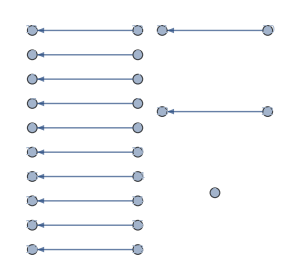
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss1,NetSize->300,SSSMax->10,SSSSize->20]
```

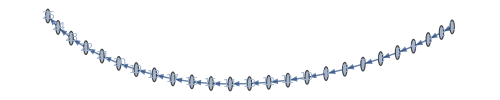
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
SSSDisplay[sss20,NetSize->500,SSSMax->10,SSSSize->100]
```

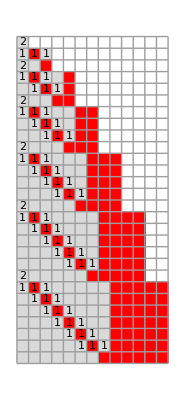


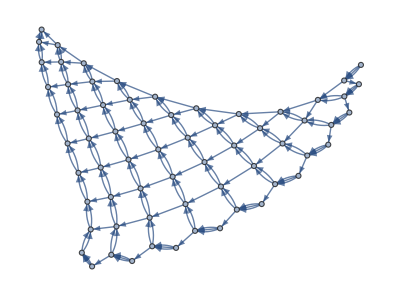
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss90,SSSMax->28,NetMax->65,NetSize->{Automatic,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True]
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
CheckDimension[l_List]:=Module[{diffs={l,Differences@l},ptrn,rats,identified={False},dim=1,expdim,n=1,i=1,ans,toobig=0},
Off[General::infy];
Off[Divide::indet];
(* 3 nested loops until identified: one difference row at a time until too short, increasing clump size, increasing initial skip *) 
While[identified==={False}&&Length[diffs⟦-1⟧]/n≥4&&i≤Length[diffs⟦-1⟧]/n-3,
If[$debug,Print[{identified,"===",{False}," && ",Length[diffs⟦-1⟧]/n,"≥",4," && ",i,"≤",Length[diffs⟦-1⟧]/n-3}]];
toobig++;
If[toobig>500,If[$debug,Print["too big, something is probably wrong, quitting"]];  Break[]];
(* try to identify pattern in clump totals of this difference row *)
If[
MatchQ[ptrn=Total/@Partition[diffs⟦-1⟧⟦i;;⟧,n];
If[$debug,Print["{dim,n,i}=",{dim,n,i},", considering differences: ",ptrn]];
ptrn
,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
identified={"dim",ToString@dim,l⟦i⟧,l⟦i+1⟧-l⟦i⟧};If[n>1,If[$debug,Print["match (",ptrn,") with Partition[data,",n,"], starting at ",i]]], 
(* else look at pattern in largest positive subsequence of ratios *)
If[MatchQ[rats=LongestPositiveSubsequence[Ratios[ptrn]],{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
identified={"exp",l⟦i⟧};
expdim=First@Commonest[rats];
If[n>1,If[$debug,Print["match (",ptrn,") with Partition[data,",n,"], starting at ",i]]],
i++;If[i>Length[diffs⟦-1⟧]/n-3,n++;i=1;If[Length[diffs⟦-1⟧]/n<4,n=1;dim++;AppendTo[diffs,Differences[diffs⟦-1⟧]]]]
]
]
];
ans=Switch[identified⟦1⟧,
"dim",{identified⟦2⟧,{identified⟦3⟧,If[identified⟦2⟧=="1",identified⟦4⟧,∞]},Grid[diffs]},
"exp",{"exp",(* ToString[expdim], *)  {identified⟦2⟧,∞},Grid[diffs],Ratios[ptrn]/.ComplexInfinity->∞},
_,{"failed",Grid[diffs],N[Ratios[diffs⟦-1⟧]]/.ComplexInfinity->∞}];
On[General::infy];
On[Divide::indet];
ans]
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
If[$debug,Print["rules used:", rulesused1,", ",rulesused2]];
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss⟦"RulesUsed"⟧,len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]
];
```

```mathematica
Clear[MaxStateLengthPositions];
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{maxlen=0,evol=sss["Evolution"]},
(* Rest@ *)
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>maxlen,Sow[n];maxlen=StringLength[evol⟦n⟧]],
{n,1,Length[evol]}
]
],
sss⟦"RulesUsed"⟧]
];
```

```mathematica
sss90["Evolution"]⟦1;;12⟧
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB}

```mathematica
CheckDimension@MaxStateLengthPositions[sss90]
```

{2,{2,∞},2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

If the sessie is repeating MaxStateLengthPositions stops by or before the first repeat, and can't be used to check dimension:

```mathematica
sss1["Verdict"]
```

Repeating

```mathematica
MaxStateLengthPositions[sss1]
```

{1}

```mathematica
CheckDimension@%
```

{failed,1
,{}}

```mathematica
CheckDimension@MaxStateLengthPositions[sss20]
```

{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

If the sessie grows exponentially, growth positions are probably frequent and unimportant.  Only cross-checking with the rule used, done by the included MergeIntervalsByRulesUsed, permits limiting consideration to significant positions:

```mathematica
CheckDimension@MaxStateLengthPositions[sssE]
```

{exp,{1,∞},1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521 | 523
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 2 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | -255 |  | ,{2,2,2,2,2,2,2,-255/128}}

```mathematica
sss90["RulesUsed"]⟦1;;30⟧
```

{2,1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1}

```mathematica
CheckDimension@LeastUsedRulePositions[sss90]
```

{2,{1,∞},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
CheckDimension@LeastUsedRulePositions[sss1]
```

{1,{1,2},1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@LeastUsedRulePositions[sss20]
```

{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
CheckDimension@LeastUsedRulePositions[sssE]
```

{exp,{1,∞},1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 |  | ,{2,2,2,2,2,2,2}}

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
```

```mathematica
sss1
```

<|Net→{2→3,4→5,6→7,8→9,10→11,12→13,14→15,16→17,18→19,20→21,22→23,24→25},OutDegreePotential→{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},OutDegreeRemaining→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},OutDegreeActual→{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},InDegree→{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},ConnectionList→{{1}→{},{}→{2},{2}→{},{}→{3},{3}→{},{}→{4},{4}→{},{}→{5},{5}→{},{}→{6},{6}→{},{}→{7},{7}→{},{}→{8},{8}→{},{}→{9},{9}→{},{}→{10},{10}→{},{}→{11},{11}→{},{}→{12},{12}→{},{}→{13},{13}→{}},Verdict→Repeating,RulesUsed→{1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1},CellsDeleted→{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}},Distance→{0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},MaxColor→6,TagIndex→14,TEvolution→{s[{0,1}],s[],s[{0,2}],s[],s[{0,3}],s[],s[{0,4}],s[],s[{0,5}],s[],s[{0,6}],s[],s[{0,7}],s[],s[{0,8}],s[],s[{0,9}],s[],s[{0,10}],s[],s[{0,11}],s[],s[{0,12}],s[],s[{0,13}],s[]},Evolution→{A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,,A,},RuleSet→{A→,→A},TRuleSet→{s[{0,lhsTag$302550_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$302550}→$SSSTagIndex+{}];s[]),s[]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{}→$SSSTagIndex+{0}];s[{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]},RuleSetWeight→2,RuleSetLength→2|>

```mathematica
sss1[#]& /@{"Verdict","Net","RulesUsed","Distance"}//Column
```

Repeating
{2→3,4→5,6→7,8→9,10→11,12→13,14→15,16→17,18→19,20→21,22→23,24→25}
{1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}
{0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
sss1["Net"]
ToNetDifferenceSets[%]
FromNetDifferenceSets[%]
```

{2→3,4→5,6→7,8→9,10→11,12→13,14→15,16→17,18→19,20→21,22→23,24→25}

{{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

{2→3,4→5,6→7,8→9,10→11,12→13,14→15,16→17,18→19,20→21,22→23,24→25}

#### SummarizeDifferenceSets: Only identifies 1-d cases

```mathematica
SummarizeDifferenceSets::usage = "SummarizeDifferenceSets[L] takes a list of sets of link lengths, as generated by ToNetDifferenceSets[net], and attempts to find a summary.";

SummarizeDifferenceSets[L:List[__List]]:=Module[{k,j,bestk=0, bestj=0},
(* L is a List of zero or more Lists *)
For[k=1, k<Length[L]/2, k++, (* k is substring length, j is offset to previous substring(s) *)
j=2k;(* pass the final subsequence *)
While[(* if still within bounds compare neighboring subsequences *)
(* 
If[j≤Length[L],Print["k = ",k,", j = ",j,", L⟦",-j,";;",-j+k-1,"⟧ = ",L⟦-j;;-j+k-1⟧, ", L⟦",-j+k,";;",-j+2k-1,"⟧ = ",L⟦-j+k;;-j+2k-1⟧,": SubsetQ? ",MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}]]];
 *)
(j≤Length[L]) && (And@@MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}]),
If[j>bestj, bestj=j; bestk=k; (* Print["new best {j,k}: ", {bestj,bestk}] *) ]; (* update best *)
j += k;  (* jump to next pair to compare *)
];
If[j>k,j-=k]; (* if possible, backup to the last good match *)
While[(* now advance backwards one at a time: RotateLeft subsequences *)
0<j≤Length[L] && -j+k-1>0 && And@@MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}],
If[j>bestj, bestj=j; bestk=k; Print["new best {j,k}: ", {bestj,bestk}]]; (* update best *)
j++
]
];
Print@{bestk, bestj};
Print["Summary: ", L⟦-bestj;;-bestj+bestk-1⟧, " : ",Round[bestj/bestk,.1]," reps = ",Round[100*bestj/Length[L],1],"%" ];
Print["Canonical: ", 
Row[{#," ⇔ ",FromNetDifferenceSets[#]}]& @ First[Sort@NestList[RotateLeft,L⟦-bestj;;-bestj+bestk-1⟧, bestk]]];
Print@Column@Partition[L⟦-bestj;;-1⟧,bestk,bestk,1,{}];
];
```

```mathematica
ToNetDifferenceSets@sss20["Net"]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
Length[ToNetDifferenceSets@sss20["Net"]]
```

24

```mathematica
SummarizeDifferenceSets@ToNetDifferenceSets@sss20["Net"]
```

{1,24}

Summary: {{1}} : 24. reps = 100%

Canonical: {{1}} ⇔ {1→2}

{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}
{{1}}

```mathematica
ToNetDifferenceSets@sss90["Net"]
```

{{1,1,1},{1,3},{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{},{1,1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
Length[ToNetDifferenceSets@sss90["Net"]]
```

74

```mathematica
SummarizeDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{10,20}

Summary: {{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11}} : 2. reps = 27%

Canonical: {{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11}} ⇔ {1→2,1→2,1→2,2→3,2→3,2→12,3→4,3→4,3→14,4→5,4→5,4→15,5→6,5→6,5→16,6→7,6→7,6→17,7→8,7→8,7→18,8→9,8→9,8→19,9→10,9→10,9→20,10→11,10→11,10→21}

{{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11}}
{{},{1,1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

### Old Code

#### Identification strategies

1.  If $SSSTEvolution stops changing (last 2 elements are equal), the SSS is Dead, as of the first instance of the repetition.  If the SSS is Dead, so is the network.  [Done]

2a.  If any two elements of $SSSEvolution are the same, the SSS is Repeating, and will repeat from then on.  Note:  for efficency, we only test whether the last element is repeated anywhere before.  Since the test happens every step, it will catch the first time it happens, and assign a value to $SSSVerdict, which remains until reinitialized.  If the SSS is Repeating, so is the network.  [Done]

2b.  If Repeating, also look for unused rules (in the repeating part):  possible long-jump.  This is implemented in TestForUnusedRules.  [Need to check.]

3.  Having “enough” repetitions in $SSSHistory sets $SSSVerdict to Pseudorepeating, meaning the SSS may be repeating, n-dimensional, or exponential.  Before this happens there’s no point in applying additional tests to the SSS or its network.  [Done]

Possible strategies:

4.  Old network test (should be reinvoked?):  Take a section of $SSSNet including 500 consecutive nodes, and look for matches elsewhere in $SSSNet.  An identical match gives a high probability of a 1-d network, even though the SSS never repeats.  (Better:  require 5 matches)

5.  If a large segment of $SSSRuleUsage repeats, it is likely that the network is repeating.  Even if exact repetition does not occur, find the positions where the least frequently used rule was used and try to fit that data to a polynomial or exponential curve and/or identify the pattern from repeated differences and ratios of differences.  (NOTE:  It is currently unclear whether an exponential fit for this data implies an exponential network.  Look at apparent exponential cases, including NKS 91e, comparing the SSS behavior and the network behavior. Caution:  many exponential networks use the same rule or subset of rules for a long time before a different rule can be applied again.)  To decrease the likelihood of incorrect identification, require at least 500 steps of evolution and that the last 90% of $SSSRuleUsage repeats, including 5 repetitions, and merge intervals before testing.  [Implementing as MinRulePositions.]

6.  In working with intervals, such as above, always make sure each interval uses the same rules, working backward from the last completed interval:  if a change occurs, adjust or merge intervals.  If n^th interval uses fewer rules than the (n-1)^st, merge the n^th with whatever follows.  If n^th interval uses more rules than the (n-1)^st, merge the (n-1)^st with whatever precedes it.  If the number of prospective intervals falls below 5, abandon attempt.  [Implementing as MergeIntervals.]

7.  Look for a pattern in the positions of the commonest element of $SSSHistory.  Since the addition of the tag (4^th part of each element, set to increment or decrement to avoid false positives when pre- or post-match strings are changing length), the commonest element is likely to have a 0 tag, and may follow a simple pattern.  Note:  merge intervals before testing.  [Implementing as CommonestHistoryPositions.]

8.  If after 500 steps the last 90% of $SSSRuleUsage (see #5) all uses the same subset of the ruleset, whether or not the behavior can be identified, if not all rules are used in the the last 90%, it is likely that the SSS (and network) is a duplicate of an earlier case, and can be skipped or can even trigger a long-jump.  This would be highly desirable. [Need to do.]

9.  New network test:  Use $SSSOutDegreeRemaining to decide which is the first node that might have new paths leading off it.  Ideally this would be the first non-zero in the list, but Pseudorepeating (growing) SSSs may repeatedly create some cells that will never be destroyed, corresponding to some nodes that retain a non-zero value in $SSSOutDegreeRemaining, in which case it may be difficult to definitely determine the index. Tally $SSSDistance⟦1;;index⟧ to give the number of nodes (n) a distance (d) from the network origin.  (Any data past this index is probably incomplete, and should be disregarded.)  Try to fit that data to a polynomial or exponential curve and/or identify the pattern from repeated differences and ratios of differences.  [Implementing as DistanceTally.]

Note: Any identifiable pattern in the first half of $SSSOutDegreeRemaining might allow a larger index to be used, indicating a pattern among the nodes that never will be “complete”, in which case distance data could be used up to where the pattern breaks, i.e., where new branches can be expected.  OR: if there are any 1s in the first half of $SSSOutDegreeRemaining, use the position of the first 2 as the index, etc.

10.  For each n, find the last node that is a distance n from the origin, up to the index mentioned in #9.  After merging intervals, seek a pattern in these values.  [Implementing as DistanceLastPositions.]

11.  Look for a pattern in the list of positions of maximum-length states in $SSSEvolution (greatest string length seen up to that point).  [Implementing as MaxStateLengthPositions.]

12.  Consider position of match in the state string.  Does a minimum or maximum position (minimum distance from end) keep recurring?  If so, restart at first such position, skipping junk before this point in the evolution and deleting unused stuff at beginning/end of state string.

13.  Consider positions of least-frequent repeated case in last 2/3 of $SSSInDegree and and reliable part of $SSSOutDegree.

```mathematica
$SSSRuleUsage
MinRulePositions
checkDimension/@MergeIntervals/@%
MaxStateLengthPositions
checkDimension@MergeIntervals@%
DistanceLastPositions
checkDimension@MergeIntervals@%
checkDimension@DistanceTally
CommonestHistoryPositions
checkDimension@MergeIntervals@%
```

#### SSS & Net Tests

Needed functions:

```mathematica
MergeIntervals[l0_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
While[n>2,
rulesused1=Union[$SSSHistory⟦l⟦n-2⟧;;l⟦n-1⟧-1,2⟧];
rulesused2=Union[$SSSHistory⟦l⟦n-1⟧;;l⟦n⟧-1,2⟧];
If[$debug,Print["rules used:", rulesused1,", ",rulesused2]];
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
myRatios[l_List,n_Integer?Positive] := 
If[n≥Length[l],{},
ListConvolve[Flatten[{1,Table[0,{n-1}],-1}],l,{-1,1},{},Power[#2,#1]&,Times]
]
```

SSS Tests:

```mathematica
CommonestHistoryPositions := If[MatchQ[$SSSVerdict,""|"Dead"],{},
Flatten@Position[$SSSHistory,First@Commonest[$SSSHistory⟦;;Round[Length[$SSSHistory]/2,1]⟧]]]
```

```mathematica
SSSEvolve[50]
```

1

```mathematica
CommonestHistoryPositions
```

{16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126}

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{1,{16,2},16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

Net Tests:

```mathematica
DistanceLastPositions:= 
Module[{tally,pos,maxdistance,odr,z=Min[$SSSOutDegreeRemaining]},
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees,nulling out (with ∞) the first tenth so as to get past initial oddities. This hopefully advances past most nodes that will never be complete due to never-to-be deleted cells *) 

odr=ReplacePart[$SSSOutDegreeRemaining,_?(#<.1Length[$SSSOutDegreeRemaining]&)->∞];
z=Min[odr];
tally=First /@ Tally  /@ Split[odr /. _?(#≠z&)->z+1];
pos=Total[Last /@ tally⟦;;Last@Last@Position[tally,{z,Max[Last/@Cases[tally,{z,_}]]}]⟧]+1;
(* Starting at this position any node with a positive entry in $SSSOutDegreeRemaining is treated as incomplete *)
(* Find distances to them all, take the minimum distance as our maximum reliable distance *)
maxdistance=Min[$SSSDistance⟦Select[Flatten@Position[$SSSDistance,_?Positive],#≥pos&]⟧];
(* Find the position of the last instance of each distance, out to maxdistance, in $SSSDistance *) 
Last[Last[Position[$SSSDistance,#]]]& /@ Range[maxdistance]
]
```

```mathematica
checkDimension@DistanceLastPositions
```

{1,{2,2},2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
DistanceTally:= 
Module[{tally,pos,maxdistance,odr,z=Min[$SSSOutDegreeRemaining]},
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees,nulling out (with ∞) the first tenth so as to get past initial oddities. This hopefully advances past most nodes that will never be complete due to never-to-be deleted cells *) 

odr=ReplacePart[$SSSOutDegreeRemaining,_?(#<.1Length[$SSSOutDegreeRemaining]&)->∞];
z=Min[odr];
tally=First /@ Tally  /@ Split[odr /. _?(#≠z&)->z+1];

(* Starting at this position any node with a positive entry in $SSSOutDegreeRemaining is treated as incomplete *)
(* Find distances to them all, take the minimum distance as our maximum reliable distance *)

maxdistance=Min[$SSSDistance⟦Select[Flatten@Position[$SSSDistance,_?Positive],#≥pos&]⟧];
Accumulate[Last /@ Tally[Sort[Select[$SSSDistance,#≤maxdistance&]]]]
(* This gives, in order, the number of nodes a distance ≤1, ≤2, ... from the origin *)
];
```

```mathematica
checkDimension@DistanceTally
```

{1,{1,1},1 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126
1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
RiffleDistanceTally := Module[{diffs,rats,identified=False,n,data=Differences[DistanceTally],mx},
Off[Power::infy,Infinity::indet,Power::indet];
mx=Length[data];
n=1;
While[identified===False && n≤mx,
If[MatchQ[diffs=Differences[data,1,n],
{Repeated[_,{0,5}],Repeated[b_,{4,∞}],Repeated[_,{0,3}]}],
identified="2",
If[MatchQ[rats=myRatios[diffs,n],
{Repeated[_,{0,5}],Repeated[b_,{3,∞}],Repeated[_,{0,3}]}],
identified="exp",
n++]
]
];
On[Power::infy,Infinity::indet,Power::indet];
Switch[identified,
False,{"failed"},
"exp",{"exp"," riffling by ",n,": ",rats},
"2",{"2"," riffling by ",n,": ",diffs}
]
]
```

```mathematica
RiffleDistanceTally
```

{2, riffling by ,1,: ,{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Differences[DistanceTally]
```

{1,2,3,5,7,10,13}

```mathematica
Differences[Differences[DistanceTally],1,2]
```

{2,3,4,5,6}

```mathematica
Differences@%
```

{1,1,1,1}

```mathematica
{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756}[[1;;-1;;2]]
FindSequenceFunction[%,n]
```

{1,5,29,137,503,1507,3863,8779}

1/180 (-180+534 n-253 n^2+30 n^3+65 n^4-24 n^5+8 n^6)

```mathematica
{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756}[[2;;-1;;2]]
FindSequenceFunction[%,n]
```

{2,12,65,270,890,2454,5901,12756}

1/180 (330 n-133 n^2+120 n^3+35 n^4+8 n^6)

```mathematica
Differences[{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756},1,2]
Differences@%
Differences@%
Differences@%
Differences@%
Differences@%
```

{4,10,24,53,108,205,366,620,1004,1564,2356,3447,4916,6855}

{6,14,29,55,97,161,254,384,560,792,1091,1469,1939}

{8,15,26,42,64,93,130,176,232,299,378,470}

{7,11,16,22,29,37,46,56,67,79,92}

{4,5,6,7,8,9,10,11,12,13}

{1,1,1,1,1,1,1,1,1}

```mathematica
Differences[{1,2,5,12,29,65,137,270,503,890,1507,2454},1,2]
Differences@%
Differences@%
Differences@%
Differences@%
Differences@%
```

{4,10,24,53,108,205,366,620,1004,1564}

{6,14,29,55,97,161,254,384,560}

{8,15,26,42,64,93,130,176}

{7,11,16,22,29,37,46}

{4,5,6,7,8,9}

{1,1,1,1,1}

#### This shows that I must extend RiffleDistanceTally to do the same sort of multiline operation that checkDimension already does! ####

#### IdentifyPseudorepeating

```mathematica
$debug=False
```

False

```mathematica
IdentifyPseudorepeating := Module[{sssAns,distanceTallyAns,sssSummary,distanceTallySummary},
Which[
$SSSVerdict=="Dead", Return[{}],

10Max[$SSSNet/.Rule->List]<Length[$SSSEvolution],
If[$debug,Print[n,". ",rs," : No network after step ",Max[$SSSNet/.Rule->List],", now at ",Length[$SSSEvolution]]];
Return[{}]
];
sssAns=checkDimension/@MergeIntervals /@ MinRulePositions;
sssAns=Which[
Length[sssAns]==0,{"failed"},
Length[sssAns]== 1,sssAns⟦1⟧,
!(Equivalent@@sssAns⟦All,1⟧),{"failed"},
Equivalent@@sssAns⟦All,1⟧, {sssAns⟦1,1⟧,First[Sort[sssAns⟦All,2;;3⟧]]},
True,{"failed"}
];
sssAns={
sssAns, (* simplified ans from MinRulePositions *)
checkDimension@MergeIntervals@MaxStateLengthPositions,
checkDimension@MergeIntervals@CommonestHistoryPositions,
checkDimension@MergeIntervals@DistanceLastPositions
}; (* combine with results of the other tests *)

If[$debug,Print[sssAns]]; 

sssSummary=Select[sssAns,First[#]≠"failed"&];
If[Length[sssSummary]>0,
sssSummary=sssSummary⟦All,1;;2⟧;
If[!(Equivalent@@(First/@sssSummary)),
If[$debug,Print["SSS tests give different answers: ", sssSummary];Print[sssAns]];sssSummary={}
]
];

If[$debug,Print["sssSummary: ",sssSummary]]; 

distanceTallyAns = {checkDimension@DistanceTally,RiffleDistanceTally};

(*
If[Length[sssSummary]>0 && sssSummary⟦1,1⟧=="1", (* DistanceTally & RiffleDistanceTally catastrophically fail for 1-d *)
distanceTallyAns={{"1","overriding!"}},
distanceTallyAns = {checkDimension@DistanceTally,RiffleDistanceTally}
];  
*)

If[$debug,Print["distanceTallyAns: ",distanceTallyAns]];

distanceTallySummary = Union[Select[First /@ distanceTallyAns,#≠"failed"&]];

If[$debug,Print["distanceTallySummary: ",distanceTallySummary]]; 


If[Length[distanceTallySummary]>0 && distanceTallySummary[[1]]=="1",distanceTallySummary={"1"}];  (* remove this kludge when function is extended, currently RiffleDistanceTally  *)

If[Length[distanceTallySummary]==2,
If[$debug,Print["Error: checkDimension@DistanceTally and RiffleDistanceTally disagree:  "]; Print[distanceTallySummary]];
distanceTallySummary={}
];

Which[
Length[distanceTallySummary]==0, 
If[$debug,Print["Distance tally tests unsuccessful"]]; {False,{sssAns,distanceTallyAns}},

Length[sssSummary]==0,
If[$debug,Print["No successful SSS tests"]];
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,$SSSRepetitionInterval,$SSSRepetitionStart}={distanceTallySummary⟦1⟧,∞,∞}
];
{True,distanceTallySummary⟦1⟧<>"qq"},

Length[sssSummary]==1 && sssSummary⟦1,1⟧== distanceTallySummary⟦1⟧,
If[$debug,Print["Only one successful SSS test"]]; 
If[$SSSVerdict=!="Repeating",{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}=sssSummary⟦1⟧];
{True,sssSummary⟦1⟧/.s_String:>s<>"q"},

Union[First/@sssSummary,distanceTallySummary]≠Union[distanceTallySummary],
If[$debug,Print["CAUTION: SSS tests and distance tally tests disagree: ",{First/@sssSummary,distanceTallySummary}]]; 
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}=Sort[sssSummary]⟦1⟧;
$SSSVerdict=distanceTallySummary⟦1⟧<>"x"<>Sort[sssSummary]⟦1,1⟧
];
{True,distanceTallySummary⟦1⟧<>"x"<>Sort[sssSummary]⟦1,1⟧,Sort[sssSummary]⟦1,2;;⟧},

True,
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}=Sort[sssSummary]⟦1⟧
];
{True,Sort[sssSummary]⟦1⟧}
]
];
```

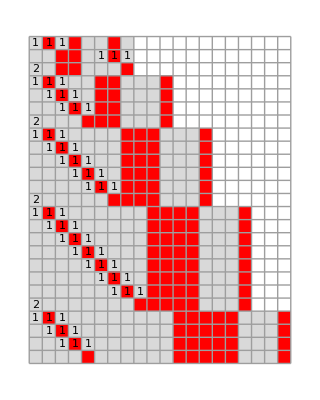
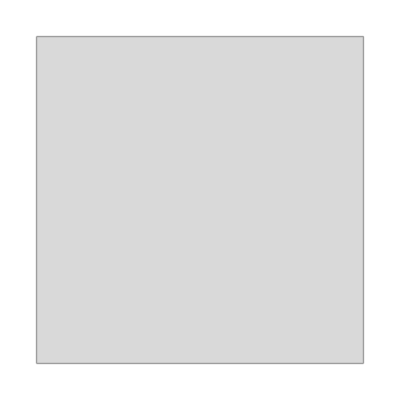
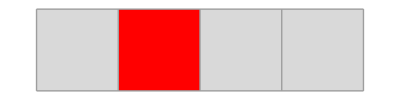
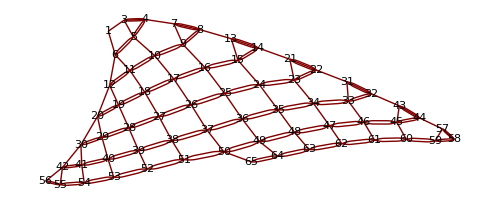
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"ABA"->"AAB","A"->"ABAA"}, "ABABAABA",75,EarlyReturn->True,SSSMax->25,NetMax->65,NetSize->500]
```

```mathematica
SSSEvolve[50]
```

Pseudorepeating

```mathematica
IdentifyPseudorepeating
```

match ({3,3,3,3,-8,-1,-1,-1,-1,-1}) with Partition[data,2], starting at 1

{True,{2,{3,∞}}}

```mathematica
SSSEvolve[10]
IdentifyPseudorepeating
```

2

{{2,{3,∞},3 | 7 | 13 | 21 | 31 | 43 | 57 | 73
4 | 6 | 8 | 10 | 12 | 14 | 16 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{4,∞},4 | 8 | 14 | 22 | 32 | 44 | 58 | 74
4 | 6 | 8 | 10 | 12 | 14 | 16 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{failed,1
,{}},{failed,6 | 12 | 20 | 30 | 42 | 56
6 | 8 | 10 | 12 | 14 | 
2 | 2 | 2 | 2 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}}}

sssSummary: {{2,{3,∞}},{2,{4,∞}}}

distanceTallyAns: {{failed,1 | 3 | 7 | 12 | 19 | 27 | 37
2 | 4 | 5 | 7 | 8 | 10 | 
2 | 1 | 2 | 1 | 2 |  | 
-1 | 1 | -1 | 1 |  |  | 
2 | -2 | 2 |  |  |  | ,{-1.,-1.}},{2, riffling by ,2,: ,{3,3,3,3}}}

distanceTallySummary: {2}

{True,{2,{3,∞}}}

```mathematica
SSSEvolve[100]
IdentifyPseudorepeating
```

2

{{2,{3,∞},3 | 7 | 13 | 21 | 31 | 43 | 57 | 73 | 91 | 111 | 133 | 157 | 183
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{4,∞},4 | 8 | 14 | 22 | 32 | 44 | 58 | 74 | 92 | 112 | 134 | 158 | 184
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{43,∞},43 | 57 | 73 | 91 | 111 | 133 | 157 | 183
14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{6,∞},6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }}

sssSummary: {{2,{3,∞}},{2,{4,∞}},{2,{43,∞}},{2,{6,∞}}}

match ({3,3,3,3,3}) with Partition[data,2], starting at 1

distanceTallyAns: {{2,{1,∞},1 | 3 | 7 | 12 | 19 | 27 | 37 | 48 | 61 | 75 | 91 | 108
2 | 4 | 5 | 7 | 8 | 10 | 11 | 13 | 14 | 16 | 17 | 
2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 |  | },{2, riffling by ,2,: ,{3,3,3,3,3,3,3,3,3}}}

distanceTallySummary: {2}

{True,{2,{3,∞}}}

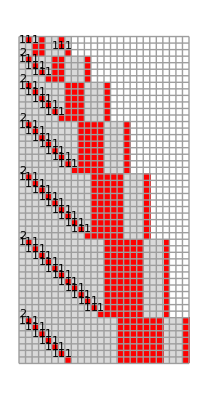
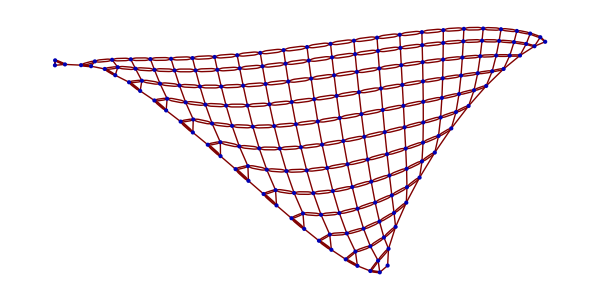
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[SSSMax->50,NetSize->{600,300},VertexLabeling->Tooltip]
```

```mathematica
DistanceTally
```

{1,3,6,10,16,23,31,40,50,61,73,86,100,115,131,148,166,185}

```mathematica
checkDimension@%
```

{dim,2,1 | 3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
2 | 3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
{2,2,2,"failed","failed","failed"}
```